```mathematica
(*問題１*)
RandomInteger[{1,100},50]
Union[%]
Select[%,PrimeQ]
Length[%]
(* Lengthを使って、個数と同じ数字を求められるけど、
カウントと言えば今考えるのはFor文の形のものです*)
```

{38,69,77,43,15,44,88,79,5,5,1,8,3,96,1,43,26,9,44,26,100,19,33,73,92,74,70,51,19,99,30,74,50,43,48,45,9,63,32,70,26,12,21,34,83,58,17,52,76,88}

{1,3,5,8,9,12,15,17,19,21,26,30,32,33,34,38,43,44,45,48,50,51,52,58,63,69,70,73,74,76,77,79,83,88,92,96,99,100}

{3,5,17,19,43,73,79,83}

8

```mathematica
Clear["Global`*"]
```

```mathematica
(*問題2*)
```

```mathematica
a={1,2,3,4,5,6};
b={1,-1,1,-1,1,-1};
Table[a.RotateLeft[b,k],{k,0,5}]
```

{-3,3,-3,3,-3,3}

```mathematica
Clear["Global`*"]
```

```mathematica
(*問題3*)
f=x/(Exp[x]-1);
a=Normal[Series[f,{x,0,10}]];
b=CoefficientList[a,x];
c=b Table[n!,{n,0,10}]
```

{1,-1/2,1/6,0,-1/30,0,1/42,0,-1/30,0,5/66}

```mathematica
(*検算*)
Clear["Global`*"]
```

```mathematica
Table[BernoulliB[x],{x,0,10}]
```

{1,-1/2,1/6,0,-1/30,0,1/42,0,-1/30,0,5/66}

```mathematica
Clear["Global`*"]
```

```mathematica
(*問題4*)
PolyhedronData[20]
```

{{Antiprism,9},ElongatedTriangularGyrobicupola,ElongatedTriangularOrthobicupola,GreatIcosahedron,GyroelongatedTriangularCupola,Icosahedron,JabulaniPolyhedron,JessensOrthogonalIcosahedron,MetabiaugmentedDodecahedron,ParabiaugmentedDodecahedron,RhombicIcosahedron,TetrahedronFiveCompound,TriangularHebesphenorotunda}

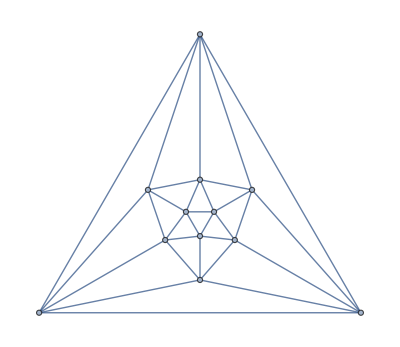

```mathematica
PolyhedronData["Icosahedron","Skeleton"]
```

```mathematica
PolyhedronData["Icosahedron"]
```

-Graphics3D-